```mathematica
Needs["ExperimentEvaluation`"]
SetDirectory["~"];
problemRewrite={"gp.demo.SymbolicRegression"->"1D","gp.demo.SymbolicRegression2D"->"2D","gp.demo.SymbolicRegression3D"->"3D","gp.demo.SymbolicRegression4D"->"4D","gp.demo.Maze"->"M1","gp.demo.MazeRangeFinders"->"M2"};
solverLabelRewrite={"SOLVER",{"GPAT"->"AT","GP"->"G","NEAT"->"N"}};
functionImplRewrite={"gpat.ATFunctions$"->"N","gpat.ATFunctionsNoConsts$"->"NC","gpat.ATFunctionsLikeGP$"->"GP","gpat.ATFunctionsLocks$"->"L"};
functionImplLabelRewrite={"GPAT.FUNCTION_IMPL",functionImplRewrite};
distanceLabelRewrite={"GPAT.DISTANCE",{"GENERAL"->"G","BASIC"->"I","ISO"->"D","PHENO"->"P","RANDOM"->"R","NODES"->"N","Null"->""}};
distanceGeneralKLabelRewrite={"GP.DISTANCE_GENERAL_K",{}};
distanceGeneralAlphaLabelRewrite={"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES",{"true"->"1","false"->"0"}};
distanceGeneralBetaLabelRewrite={"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT",{"true"->"1","false"->"0"}};
distanceGeneralC1LabelRewrite={"GPAT.DISTANCE_C1",{}};
distanceGeneralC2LabelRewrite={"GPAT.DISTANCE_C2",{}};
distanceGeneralCACTLabelRewrite={"GPAT.DISTANCE_CACT",{}};
plotRange={All,{0,100}};
listOfDirectProblems=Grid[{{#[[1]]},{Style[TraditionalForm[#[[2]]],FontSize->12]}}]&/@{{"1D-F",1.5 Subscript[x, 1]^3+2.3 Subscript[x, 1]^2-1.1 Subscript[x, 1]+3.7},{"1D-H",0.1 Subscript[x, 1]^2+0.2Sin[Subscript[x, 1]]},{"2D-I",1.5 Subscript[x, 1] Subscript[x, 2]^2+2.3 Subscript[x, 1] Subscript[x, 2]-1.1 Subscript[x, 2]^2},{"2D-K",Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1] Subscript[x, 2]-Subscript[x, 2]^2},{"3D-E",1.5 Subscript[x, 1] Subscript[x, 2]+2.3 Subscript[x, 1]+Subscript[x, 2] Subscript[x, 3]-1.1 Subscript[x, 3]},{"3D-H",1.5 Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3]+2.3 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3]-1.1 Subscript[x, 2]+5.3},{"3D-K",Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 2]+Subscript[x, 2] Subscript[x, 3]},{"4D-C",1.5 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3] Subscript[x, 4]},{"4D-F",1.5 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3]+2.3 Subscript[x, 1]-1.1 Subscript[x, 2]-1.1 Subscript[x, 4]},{"4D-G",1.5 Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3] Subscript[x, 4]+2.3 Subscript[x, 1]-1.1 Subscript[x, 2]},{"4D-V",Exp[-1.36709 Subscript[x, 2]^2] Subscript[x, 1](2.43454 Exp[-Subscript[x, 3]^2] -0.393788 Sin[1-Subscript[x, 1]])},{"MAZE-1",""},{"MAZE-2",""}};
listOfDirectProblems={"1D-F","1D-H","2D-I","2D-K","3D-E","3D-H","3D-K","4D-C","4D-F","4D-G","4D-V","MAZE-1","MAZE-2"};
listOfIndirectProblems={"Bit Reverse","Bit Shift","Bit Rotate","Parity","Visual Discrimination","Mobile Robot Navigation"};
```

```mathematica
a=8.1;
b=5.6;
all=600;
testFisherExact[{{0.01a all,all-0.01a all},{0.01b all,all-0.01b all}}]
```

0.109128

## Experiments GPAT Direct Innovation Numbers

```mathematica
names={"T/AT_B","T/AT_B_NC"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE_C2","GPAT.DISTANCE_C1","GPAT.DISTANCE_CACT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite,
distanceGeneralC1LabelRewrite,
distanceGeneralC2LabelRewrite,
distanceGeneralCACTLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","RECO.GENERATOR","PROBLEM","GPAT.DISTANCE_CACT","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
printAsTable[sortedData,changingParameters[data]];
```

{GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.TARGET_FITNESS,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
parts = 81;
cellAll={};
colNumber=3;
(*parts = 27;
cellAll={};
colNumber=1;*)

selectedData=selectData[sortedData,{"PROBLEM"->{"1D"},"SYMBOLIC_REGRESSION.F"->{"F"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["1DF",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"1D"},"SYMBOLIC_REGRESSION.F"->{"H"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["1DH",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"2D"},"SYMBOLIC_REGRESSION.F"->{"I"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["2DI",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"2D"},"SYMBOLIC_REGRESSION.F"->{"K"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["2DK",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"E"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DE",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"H"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DH",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"K"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DK",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"C"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DC",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"F"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DF",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"G"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DG",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"V"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DV",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"M1"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["M1",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"M2"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["M2",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["AT_B_DIRECT.pdf",Grid[cellAll,Frame->All]];*)
Export["AT_B_DIRECT_"<>#[[1,1]]<>".pdf",Grid[{{"",Style["GPAT Innovation Numbers: Success, Constants, Nodes, Depth",FontSize->25]},#},Frame->All]]&/@cellAll
```

{AT_B_DIRECT_1DF.pdf,AT_B_DIRECT_1DH.pdf,AT_B_DIRECT_2DI.pdf,AT_B_DIRECT_2DK.pdf,AT_B_DIRECT_3DE.pdf,AT_B_DIRECT_3DH.pdf,AT_B_DIRECT_3DK.pdf,AT_B_DIRECT_4DC.pdf,AT_B_DIRECT_4DF.pdf,AT_B_DIRECT_4DG.pdf,AT_B_DIRECT_4DV.pdf,AT_B_DIRECT_M1.pdf,AT_B_DIRECT_M2.pdf}

```mathematica
parts = 27;
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
gridBDN=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBDN=Transpose[Transpose[gridBDN[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
gridBDNC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBDNC=Transpose[Transpose[gridBDNC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
gridBDGP=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBDGP=Transpose[Transpose[gridBDGP[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];

(*printAsTable[selectedData,changingParameters[data]]*)
```

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
19 | 1. | 5. | 1. | 29.0385 | 267/26
11 | 1. | 2. | 2. | 31.6923 | 11
14 | 2. | 2. | 2. | 32.3462 | 144/13
24 | 2. | 5. | 5. | 33.3077 | 305/26
22 | 2. | 5. | 1. | 28.8077 | 315/26
4 | 2. | 1. | 1. | 33.1538 | 335/26
13 | 2. | 2. | 1. | 31.0385 | 168/13
26 | 5. | 5. | 2. | 31.5385 | 171/13
10 | 1. | 2. | 1. | 32.3077 | 349/26
16 | 5. | 2. | 1. | 30.8462 | 175/13
25 | 5. | 5. | 1. | 29.6154 | 177/13
1 | 1. | 1. | 1. | 31.8077 | 178/13
20 | 1. | 5. | 2. | 32.5769 | 179/13
15 | 2. | 2. | 5. | 32.8846 | 359/26
6 | 2. | 1. | 5. | 34.4231 | 189/13
23 | 2. | 5. | 2. | 32.6538 | 379/26
17 | 5. | 2. | 2. | 33.0769 | 190/13
21 | 1. | 5. | 5. | 33.9615 | 191/13
27 | 5. | 5. | 5. | 33.4231 | 194/13
3 | 1. | 1. | 5. | 33.6923 | 389/26
9 | 5. | 1. | 5. | 33.8846 | 196/13
12 | 1. | 2. | 5. | 34.2308 | 204/13
8 | 5. | 1. | 2. | 34.7692 | 204/13
2 | 1. | 1. | 2. | 34.8077 | 409/26
18 | 5. | 2. | 5. | 34.1923 | 427/26
5 | 2. | 1. | 2. | 34.7692 | 439/26
7 | 5. | 1. | 1. | 35.0769 | 449/26

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
22 | 2. | 5. | 1. | 18.8462 | 279/26
12 | 1. | 2. | 5. | 20.2692 | 289/26
23 | 2. | 5. | 2. | 19.6538 | 297/26
13 | 2. | 2. | 1. | 19.5385 | 301/26
19 | 1. | 5. | 1. | 18.6923 | 307/26
20 | 1. | 5. | 2. | 19.1538 | 311/26
25 | 5. | 5. | 1. | 18.4615 | 319/26
3 | 1. | 1. | 5. | 20.0385 | 162/13
6 | 2. | 1. | 5. | 20.0385 | 329/26
21 | 1. | 5. | 5. | 19.8462 | 166/13
10 | 1. | 2. | 1. | 19.8462 | 168/13
14 | 2. | 2. | 2. | 20.5 | 176/13
7 | 5. | 1. | 1. | 20.0769 | 355/26
16 | 5. | 2. | 1. | 19.0769 | 369/26
15 | 2. | 2. | 5. | 20.8462 | 29/2
2 | 1. | 1. | 2. | 20.1538 | 189/13
1 | 1. | 1. | 1. | 20.4231 | 190/13
17 | 5. | 2. | 2. | 20.7308 | 191/13
11 | 1. | 2. | 2. | 20.2692 | 15
24 | 2. | 5. | 5. | 20.7308 | 395/26
8 | 5. | 1. | 2. | 20.1923 | 401/26
27 | 5. | 5. | 5. | 20.5769 | 206/13
26 | 5. | 5. | 2. | 20.0769 | 421/26
4 | 2. | 1. | 1. | 20.5 | 218/13
18 | 5. | 2. | 5. | 20.8846 | 445/26
5 | 2. | 1. | 2. | 21.2308 | 227/13
9 | 5. | 1. | 5. | 21.0769 | 457/26

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
22 | 2. | 5. | 1. | 32.3462 | 217/26
19 | 1. | 5. | 1. | 31.1923 | 217/26
2 | 1. | 1. | 2. | 32.0385 | 255/26
23 | 2. | 5. | 2. | 32.9615 | 265/26
21 | 1. | 5. | 5. | 32.2692 | 269/26
12 | 1. | 2. | 5. | 30.8462 | 140/13
25 | 5. | 5. | 1. | 33.1154 | 283/26
16 | 5. | 2. | 1. | 33.9231 | 145/13
24 | 2. | 5. | 5. | 33.7692 | 148/13
13 | 2. | 2. | 1. | 34.1923 | 313/26
3 | 1. | 1. | 5. | 31.1154 | 159/13
11 | 1. | 2. | 2. | 32.4231 | 160/13
26 | 5. | 5. | 2. | 35.0385 | 321/26
20 | 1. | 5. | 2. | 33.6154 | 329/26
15 | 2. | 2. | 5. | 33.7692 | 359/26
10 | 1. | 2. | 1. | 35.6154 | 371/26
17 | 5. | 2. | 2. | 35.2692 | 193/13
27 | 5. | 5. | 5. | 35.3462 | 389/26
14 | 2. | 2. | 2. | 36. | 409/26
4 | 2. | 1. | 1. | 36.6923 | 16
5 | 2. | 1. | 2. | 37.0385 | 35/2
1 | 1. | 1. | 1. | 37.8077 | 469/26
6 | 2. | 1. | 5. | 34.4231 | 477/26
9 | 5. | 1. | 5. | 38.0385 | 487/26
7 | 5. | 1. | 1. | 37.6538 | 249/13
18 | 5. | 2. | 5. | 37.6923 | 275/13
8 | 5. | 1. | 2. | 38.8077 | 589/26

```mathematica
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{2.},"GPAT.DISTANCE_CACT"->{5.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_B_OR_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{1.},"GPAT.DISTANCE_CACT"->{5.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_B_NC_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{1.},"GPAT.DISTANCE_CACT"->{2.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_B_GP_CHOICE"];
```

## Experiments GPAT Direct Generalized

```mathematica
names={"T/AT_G_OR","T/AT_G_GP","T/AT_G_NC"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite,
distanceGeneralKLabelRewrite,
distanceGeneralAlphaLabelRewrite,
distanceGeneralBetaLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.TARGET_FITNESS,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
parts = 36;
colNumber=3;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"1D"},"SYMBOLIC_REGRESSION.F"->{"F"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["1DF",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"1D"},"SYMBOLIC_REGRESSION.F"->{"H"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["1DH",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"2D"},"SYMBOLIC_REGRESSION.F"->{"I"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["2DI",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"2D"},"SYMBOLIC_REGRESSION.F"->{"K"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["2DK",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"E"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DE",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"H"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DH",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"K"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DK",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"C"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DC",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"F"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DF",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"G"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DG",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"V"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DV",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"M1"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["M1",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"M2"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["M2",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["AT_B_DIRECT.pdf",Grid[cellAll,Frame->All]];*)
Export["AT_G_DIRECT_"<>#[[1,1]]<>".pdf",Grid[{{"",Style["GPAT Generalized: Success, Constants, Nodes, Depth",FontSize->25]},#},Frame->All]]&/@cellAll
```

{AT_G_DIRECT_1DF.pdf,AT_G_DIRECT_1DH.pdf,AT_G_DIRECT_2DI.pdf,AT_G_DIRECT_2DK.pdf,AT_G_DIRECT_3DE.pdf,AT_G_DIRECT_3DH.pdf,AT_G_DIRECT_3DK.pdf,AT_G_DIRECT_4DC.pdf,AT_G_DIRECT_4DF.pdf,AT_G_DIRECT_4DG.pdf,AT_G_DIRECT_4DV.pdf,AT_G_DIRECT_M1.pdf,AT_G_DIRECT_M2.pdf}

```mathematica
parts = 12;
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
gridGDN=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGDN=Transpose[Transpose[gridGDN[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
gridGDGP=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGDGP=Transpose[Transpose[gridGDGP[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
gridGDNC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGDNC=Transpose[Transpose[gridGDNC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
(*printAsTable[selectedData,changingParameters[data]]*)
```

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
11 | true | 10. | false | 16.3846 | 36/13
12 | true | 10. | true | 17.1538 | 40/13
7 | true | 2. | false | 21.3846 | 50/13
8 | true | 2. | true | 29.6154 | 167/26
10 | false | 10. | true | 21.9231 | 90/13
9 | false | 10. | false | 22.0385 | 92/13
3 | true | 1. | false | 31.0385 | 94/13
5 | false | 2. | false | 23.2692 | 96/13
6 | false | 2. | true | 24.8462 | 15/2
4 | true | 1. | true | 36.4231 | 205/26
1 | false | 1. | false | 29.1154 | 115/13
2 | false | 1. | true | 30.3846 | 235/26

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
1 | false | 1. | false | 6.46154 | 121/26
10 | false | 10. | true | 8.57692 | 123/26
2 | false | 1. | true | 6.96154 | 62/13
9 | false | 10. | false | 8.07692 | 69/13
5 | false | 2. | false | 8.61538 | 153/26
12 | true | 10. | true | 13.6154 | 167/26
6 | false | 2. | true | 8.84615 | 179/26
11 | true | 10. | false | 15.0769 | 183/26
4 | true | 1. | true | 16.1154 | 189/26
8 | true | 2. | true | 16.1923 | 95/13
3 | true | 1. | false | 17.2308 | 229/26
7 | true | 2. | false | 19.8077 | 116/13

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
6 | false | 2. | true | 10.5 | 72/13
12 | true | 10. | true | 16.4615 | 75/13
1 | false | 1. | false | 10.7692 | 153/26
11 | true | 10. | false | 16.7308 | 6
5 | false | 2. | false | 11.2692 | 157/26
7 | true | 2. | false | 17.9615 | 80/13
10 | false | 10. | true | 10.8462 | 81/13
9 | false | 10. | false | 10.7692 | 171/26
3 | true | 1. | false | 19.7308 | 90/13
8 | true | 2. | true | 19.8846 | 193/26
2 | false | 1. | true | 8.80769 | 99/13
4 | true | 1. | true | 21.1923 | 102/13

```mathematica
grid=Join[gridGDN,gridGDGP,gridGDNC];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(true | 1. | true | 2.66667
true | 1. | false | 4.
false | 1. | true | 4.33333
true | 2. | true | 5.
true | 2. | false | 6.
false | 2. | false | 7.
false | 10. | false | 7.
false | 2. | true | 7.33333
false | 1. | false | 8.
false | 10. | true | 8.33333
true | 10. | false | 8.66667
true | 10. | true | 9.66667)

```mathematica
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"false"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_G_OR_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"},"GP.DISTANCE_GENERAL_K"->{2.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_G_GP_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"true"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_G_NC_CHOICE"];
```

## Experiments GPAT Direct Random

```mathematica
names={"T/AT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","RECO.GENERATOR","GP.DISTANCE","SOLVER"}];
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.TARGET_FITNESS,ID,MAZE.MAP,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
parts = 3;
colNumber=3;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"1D","2D","3D","4D","M1","M2"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["AT_R_DIRECT.pdf",Grid[{{Style["GPAT Random Direct: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]

(*Export["AT_G_DIRECT_"<>#[[1,1]]<>".pdf",Grid[{{"", "GPAT Generalized",FontSize->25]},#},Frame->All]]&/@cellAll*)
```

AT_R_DIRECT.pdf

```mathematica
printBooleanRanksAsTable[selectedData,"SUCCESS",3]
```

ID | GPAT.FUNCTION_IMPL | RANK
3 | NC | 37/26
1 | GP | 23/13
2 | N | 73/26

## Experiments GPEFS Direct Generalized

```mathematica
names={"T/GP_GPEFS_GENERAL_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC",("PARALLEL.FORCE_THREADS"->_)->("PARALLEL.FORCE_THREADS"->1)}];
epilog={Text[Style[Grid[{{"C"},{"α"},{"β"}},Spacings->{2,0}],Bold,FontSize->15],{0.7,-12}]};
padding={{30,0},{75,30}};
sortedData = sortDataByParams[data,{"ID","PROBLEM","SYMBOLIC_REGRESSION.F","SOLVER","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
{"GP.DISTANCE_GENERAL_C",{"."->""}},
{"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT",{"false"->"0","true"->"1"}},
{"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES",{"false"->"0","true"->"1"}}
}];
sortedData=replaceLabels[sortedData,newLabels];
changingParameters[data]
printAsTable[sortedData,changingParameters[data]~Complement~{"GPAT.DISTANCE_PHENO_HIGH","GPAT.DISTANCE_PHENO_LOW","GPAT.DISTANCE_PHENO_STEPS","PARALLEL.FORCE_THREADS","GP.TARGET_FITNESS"}];
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.DISTANCE_GENERAL_C,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.TARGET_FITNESS,ID,MAZE.MAP,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
parts = 24;
gridEFSGD=printBooleanRanksAsTable[sortedData,"SUCCESS",parts]
gridEFSGD=Transpose[Transpose[gridEFSGD[[1,2;;All,2;;5]]]~Join~{Array[parts+1-#&,parts]}];
```

ID | GP.DISTANCE_GENERAL_C | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
24 | 1. | true | 10. | true | 16.5 | 18/7
18 | 1. | false | 10. | false | 17.1071 | 81/28
22 | 1. | true | 10. | false | 16.8214 | 87/28
20 | 1. | false | 10. | true | 18.1071 | 99/28
16 | 1. | true | 2. | true | 25.8214 | 50/7
12 | 1. | false | 2. | true | 26.2857 | 51/7
19 | 0. | false | 10. | true | 37.7857 | 127/14
17 | 0. | false | 10. | false | 37.7143 | 67/7
23 | 0. | true | 10. | true | 39.6071 | 303/28
21 | 0. | true | 10. | false | 39.6429 | 321/28
10 | 1. | false | 2. | false | 42.1786 | 355/28
15 | 0. | true | 2. | true | 47.6071 | 179/14
11 | 0. | false | 2. | true | 46.75 | 187/14
7 | 0. | true | 1. | true | 58.2143 | 201/14
4 | 1. | false | 1. | true | 58.7143 | 103/7
8 | 1. | true | 1. | true | 59.2857 | 211/14
3 | 0. | false | 1. | true | 59.8214 | 423/28
13 | 0. | true | 2. | false | 58.9286 | 219/14
14 | 1. | true | 2. | false | 59.2857 | 33/2
9 | 0. | false | 2. | false | 52.6786 | 69/4
1 | 0. | false | 1. | false | 65.6071 | 41/2
2 | 1. | false | 1. | false | 67.1786 | 85/4
6 | 1. | true | 1. | false | 67.9643 | 601/28
5 | 0. | true | 1. | false | 67.8929 | 153/7

```mathematica
grid=Join[gridGDN,gridGDGP,gridGDNC];
SortBy[Mean/@GatherBy[gridEFSGD,#[[1;;4]]&],#[[5]]&]//N//MatrixForm
```

(0. | true | 1. | false | 1.
1. | true | 1. | false | 2.
1. | false | 1. | false | 3.
0. | false | 1. | false | 4.
0. | false | 2. | false | 5.
1. | true | 2. | false | 6.
0. | true | 2. | false | 7.
0. | false | 1. | true | 8.
1. | true | 1. | true | 9.
1. | false | 1. | true | 10.
0. | true | 1. | true | 11.
0. | false | 2. | true | 12.
0. | true | 2. | true | 13.
1. | false | 2. | false | 14.
0. | true | 10. | false | 15.
0. | true | 10. | true | 16.
0. | false | 10. | false | 17.
0. | false | 10. | true | 18.
1. | false | 2. | true | 19.
1. | true | 2. | true | 20.
1. | false | 10. | true | 21.
1. | true | 10. | false | 22.
1. | false | 10. | false | 23.
1. | true | 10. | true | 24.)

```mathematica
selectedData=selectData[sortedData,{"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_C"->{0.},"GP.DISTANCE_GENERAL_K"->{1.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"GP_GPEFS_GENERAL_CHOICE_GECCO"];
```

## Experiments Direct Best/Choice

```mathematica
names={"T/NEAT","T/GP","T/AT_G_OR_BEST","T/AT_G_OR_CHOICE","T/AT_G_GP_BEST","T/AT_G_GP_CHOICE","T/AT_G_NC_BEST","T/AT_G_NC_CHOICE","T/AT_B_OR_BEST","T/AT_B_OR_CHOICE","T/AT_B_NC_BEST","T/AT_B_NC_CHOICE","T/AT_B_GP_BEST","T/AT_B_GP_CHOICE","T/GP_GPEFS_GENERAL_BEST_GECCO","T/GP_GPEFS_GENERAL_CHOICE_GECCO"};
names={"T/NEAT","T/GP","T/AT_G_OR_BEST","T/AT_G_GP_BEST","T/AT_G_NC_BEST","T/AT_B_OR_BEST","T/AT_B_NC_BEST","T/AT_B_GP_BEST","T/AT_R","T/GP_GPEFS_GENERAL_BEST_GECCO"};
(*names={"T/NEAT","T/GP","T/AT_G_OR_CHOICE","T/AT_G_GP_CHOICE","T/AT_G_NC_CHOICE","T/AT_B_OR_CHOICE","T/AT_B_NC_CHOICE","T/AT_B_GP_CHOICE","T/AT_R","T/GP_GPEFS_GENERAL_CHOICE_GECCO"};*)
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=removeData[sortedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}];
printAsTable[sortedData,{"SOLVER","ID","VARIANT","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_C,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TARGET_FITNESS,GP.TYPE,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SOLVER,SYMBOLIC_REGRESSION.F}

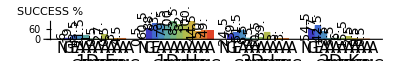

ALL_BEST_DIRECT_1D_2D.pdf

```mathematica
parts = 12;
colNumber=12;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"1D","2D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["ALL_CHOICE_DIRECT_1D_2D.pdf",Grid[{{Style["GPAT CHOICE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]*)
Export["ALL_BEST_DIRECT_1D_2D.pdf",Grid[{{Style["GPAT BEST: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

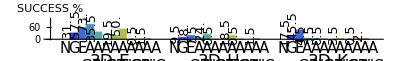

ALL_BEST_DIRECT_3D.pdf

```mathematica
parts = 12;
colNumber=12;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems[[5;;-1]],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems[[5;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems[[5;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems[[5;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["ALL_CHOICE_DIRECT_3D.pdf",Grid[{{Style["GPAT CHOICE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]*)
Export["ALL_BEST_DIRECT_3D.pdf",Grid[{{Style["GPAT BEST: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

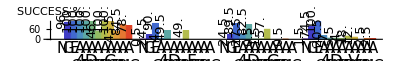

ALL_BEST_DIRECT_4D.pdf

```mathematica
parts = 12;
colNumber=12;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems[[8;;-1]],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems[[8;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems[[8;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems[[8;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["ALL_CHOICE_DIRECT_4D.pdf",Grid[{{Style["GPAT CHOICE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]*)
Export["ALL_BEST_DIRECT_4D.pdf",Grid[{{Style["GPAT BEST: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

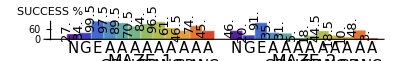

ALL_BEST_DIRECT_MAZE.pdf

```mathematica
parts = 12;
colNumber=12;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"M1","M2"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems[[12;;-1]],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems[[12;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems[[12;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems[[12;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["ALL_CHOICE_DIRECT_MAZE.pdf",Grid[{{Style["GPAT CHOICE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]*)
Export["ALL_BEST_DIRECT_MAZE.pdf",Grid[{{Style["GPAT BEST: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments Direct Aggregated Distance Choice

```mathematica
names={"T/AT_G_OR_CHOICE","T/AT_G_GP_CHOICE","T/AT_G_NC_CHOICE","T/AT_B_OR_CHOICE","T/AT_B_NC_CHOICE","T/AT_B_GP_CHOICE","T/AT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=removeData[sortedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}];
aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,13]]];
printAsTable[aggregatedData,{"SOLVER","ID","VARIANT","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.TARGET_FITNESS,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SYMBOLIC_REGRESSION.F}

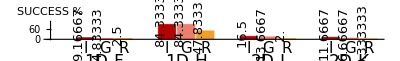

ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_1D_2D.pdf

```mathematica
parts = 3;
colNumber=3;
cellAll={};
problem={"1D","2D"};
aggregatedLabels=Flatten[Array[{"I","G","R"}&,13]];

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_1D_2D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

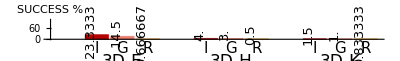

ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_3D.pdf

```mathematica
problem={"3D"};
listOfProblems=listOfDirectProblems[[5;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_3D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

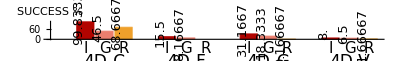

ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_4D.pdf

```mathematica
problem={"4D"};
listOfProblems=listOfDirectProblems[[8;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_4D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

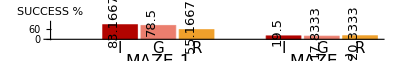

ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_MAZE.pdf

```mathematica
problem={"M1","M2"};
listOfProblems=listOfDirectProblems[[12;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_MAZE.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments Direct Aggregated Implementation Choice

```mathematica
names={"T/AT_G_OR_CHOICE","T/AT_G_GP_CHOICE","T/AT_G_NC_CHOICE","T/AT_B_OR_CHOICE","T/AT_B_NC_CHOICE","T/AT_B_GP_CHOICE","T/AT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.FUNCTION_IMPL","GPAT.DISTANCE","VARIANT"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=removeData[sortedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}];
aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,13]]];
printAsTable[aggregatedData,{"SOLVER","ID","VARIANT","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.TARGET_FITNESS,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SYMBOLIC_REGRESSION.F}

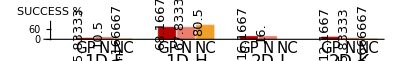

ALL_CHOICE_AGGREGATED_IMPL_DIRECT_1D_2D.pdf

```mathematica
parts = 3;
colNumber=3;
cellAll={};
problem={"1D","2D"};
aggregatedLabels=Flatten[Array[{"GP","N","NC"}&,13]];

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_IMPL_DIRECT_1D_2D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

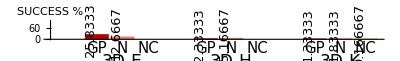

ALL_CHOICE_AGGREGATED_IMPL_DIRECT_3D.pdf

```mathematica
problem={"3D"};
listOfProblems=listOfDirectProblems[[5;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_IMPL_DIRECT_3D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

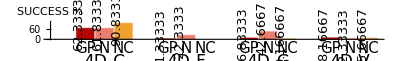

ALL_CHOICE_AGGREGATED_IMPL_DIRECT_4D.pdf

```mathematica
problem={"4D"};
listOfProblems=listOfDirectProblems[[8;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_IMPL_DIRECT_4D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

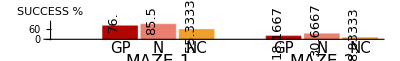

ALL_CHOICE_AGGREGATED_IMPL_DIRECT_MAZE.pdf

```mathematica
problem={"M1","M2"};
listOfProblems=listOfDirectProblems[[12;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_IMPL_DIRECT_MAZE.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments Direct NEAT Only

```mathematica
names={"T/NEAT"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=removeData[sortedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}];
printAsTable[sortedData,{"SOLVER","ID","VARIANT","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}]
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.TARGET_FITNESS,ID,MAZE.MAP,PROBLEM,SYMBOLIC_REGRESSION.F}

ID | PARAM FILE | SOLVER | ID | VARIANT | GPAT.DISTANCE | GPAT.FUNCTION_IMPL | PROBLEM | SYMBOLIC_REGRESSION.F | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | MAZE.MAP
{N} | T/NEAT/parameters_001.txt | NEAT | 1D |  |  |  | 1D | F |  |  |  | 
{N} | T/NEAT/parameters_002.txt | NEAT | 1D |  |  |  | 1D | H |  |  |  | 
{N} | T/NEAT/parameters_003.txt | NEAT | 2D |  |  |  | 2D | I |  |  |  | 
{N} | T/NEAT/parameters_004.txt | NEAT | 2D |  |  |  | 2D | K |  |  |  | 
{N} | T/NEAT/parameters_005.txt | NEAT | 3D |  |  |  | 3D | E |  |  |  | 
{N} | T/NEAT/parameters_006.txt | NEAT | 3D |  |  |  | 3D | H |  |  |  | 
{N} | T/NEAT/parameters_007.txt | NEAT | 3D |  |  |  | 3D | K |  |  |  | 
{N} | T/NEAT/parameters_008.txt | NEAT | 4D |  |  |  | 4D | C |  |  |  | 
{N} | T/NEAT/parameters_009.txt | NEAT | 4D |  |  |  | 4D | F |  |  |  | 
{N} | T/NEAT/parameters_010.txt | NEAT | 4D |  |  |  | 4D | G |  |  |  | 
{N} | T/NEAT/parameters_011.txt | NEAT | 4D |  |  |  | 4D | V |  |  |  | 
{N} | T/NEAT/parameters_012.txt | NEAT | MAZE |  |  |  | M1 |  |  |  |  | map2.csv
{N} | T/NEAT/parameters_013.txt | NEAT | MAZE |  |  |  | M2 |  |  |  |  | map4.csv

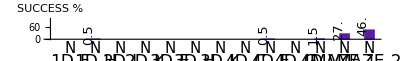

NEAT_DIRECT.pdf

```mathematica
parts = 1;
colNumber=13;
cellAll={};
selectedData=sortedData;
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN}}]}}];
Export["NEAT_DIRECT.pdf",Grid[{{Style["NEAT Direct: Success, Constants, Nodes",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments GPAT Indirect Innovation Numbers

```mathematica
names={"T/HAT_B","T/HAT_B_NC","T/HAT_B_ROBO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.DISTANCE_C1","GPAT.DISTANCE_C2","GPAT.DISTANCE_CACT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite,
distanceGeneralC1LabelRewrite,
distanceGeneralC2LabelRewrite,
distanceGeneralCACTLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","GPAT.DISTANCE_C1","GPAT.DISTANCE_C2","GPAT.DISTANCE_CACT","RECO.GENERATOR","PROBLEM"}];
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.progress,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,RECO.PATTERNS}

```mathematica
parts = 81;
cellAll={};
colNumber->3;

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCM",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCS",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCR",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"XOR"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["XOR",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"FC"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["FC",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"ROBOTS"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["ROBO",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

Export["AT_B_INDIRECT_"<>#[[1,1]]<>".pdf",Grid[{{"",Style["GPAT Innovation Numbers: Success, Constants, Nodes, Depth",FontSize->25]},#},Frame->All]]&/@cellAll
```

{AT_B_INDIRECT_rCM.pdf,AT_B_INDIRECT_rCS.pdf,AT_B_INDIRECT_rCR.pdf,AT_B_INDIRECT_XOR.pdf,AT_B_INDIRECT_FC.pdf,AT_B_INDIRECT_ROBO.pdf}

```mathematica
parts = 27;
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
gridBIN=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBIN=Transpose[Transpose[gridBIN[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
gridBINC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBINC=Transpose[Transpose[gridBINC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
gridBIGP=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBIGP=Transpose[Transpose[gridBIGP[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
```

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
5 | 1. | 2. | 2. | 55.4 | 15/2
26 | 5. | 5. | 2. | 56.4 | 42/5
10 | 2. | 1. | 1. | 57.5 | 44/5
14 | 2. | 2. | 2. | 56. | 89/10
19 | 5. | 1. | 1. | 60.1 | 99/10
13 | 2. | 2. | 1. | 57.4 | 54/5
4 | 1. | 2. | 1. | 57.3 | 12
1 | 1. | 1. | 1. | 57.8 | 63/5
25 | 5. | 5. | 1. | 61.2 | 13
8 | 1. | 5. | 2. | 57.7 | 13
16 | 2. | 5. | 1. | 58.5 | 66/5
15 | 2. | 2. | 5. | 57.2 | 139/10
23 | 5. | 2. | 2. | 60.3 | 147/10
7 | 1. | 5. | 1. | 57.2 | 15
22 | 5. | 2. | 1. | 61.9 | 79/5
18 | 2. | 5. | 5. | 59.1 | 79/5
6 | 1. | 2. | 5. | 56.6 | 79/5
27 | 5. | 5. | 5. | 60.1 | 159/10
20 | 5. | 1. | 2. | 61.4 | 159/10
3 | 1. | 1. | 5. | 57.3 | 159/10
11 | 2. | 1. | 2. | 58.1 | 16
2 | 1. | 1. | 2. | 57.2 | 33/2
24 | 5. | 2. | 5. | 59. | 83/5
21 | 5. | 1. | 5. | 59.3 | 83/5
9 | 1. | 5. | 5. | 59. | 167/10
17 | 2. | 5. | 2. | 59.6 | 97/5
12 | 2. | 1. | 5. | 57.9 | 97/5

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
25 | 5. | 5. | 1. | 35.8 | 31/5
15 | 2. | 2. | 5. | 34.4 | 36/5
16 | 2. | 5. | 1. | 36.4 | 10
13 | 2. | 2. | 1. | 36.3 | 103/10
26 | 5. | 5. | 2. | 37.1 | 53/5
7 | 1. | 5. | 1. | 37.6 | 57/5
10 | 2. | 1. | 1. | 37.6 | 23/2
23 | 5. | 2. | 2. | 36.4 | 123/10
6 | 1. | 2. | 5. | 37.3 | 123/10
11 | 2. | 1. | 2. | 37.5 | 127/10
22 | 5. | 2. | 1. | 38.5 | 129/10
1 | 1. | 1. | 1. | 38.6 | 66/5
27 | 5. | 5. | 5. | 39.1 | 14
3 | 1. | 1. | 5. | 38.3 | 141/10
24 | 5. | 2. | 5. | 38.1 | 71/5
20 | 5. | 1. | 2. | 38.2 | 73/5
14 | 2. | 2. | 2. | 38.4 | 149/10
5 | 1. | 2. | 2. | 38.5 | 151/10
9 | 1. | 5. | 5. | 39.3 | 163/10
4 | 1. | 2. | 1. | 39.8 | 167/10
12 | 2. | 1. | 5. | 39.9 | 84/5
2 | 1. | 1. | 2. | 39. | 89/5
19 | 5. | 1. | 1. | 40.1 | 181/10
8 | 1. | 5. | 2. | 39.9 | 37/2
21 | 5. | 1. | 5. | 39.8 | 93/5
18 | 2. | 5. | 5. | 40.4 | 93/5
17 | 2. | 5. | 2. | 40.5 | 191/10

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
6 | 1. | 2. | 5. | 52.4 | 39/10
3 | 1. | 1. | 5. | 47.2 | 11/2
12 | 2. | 1. | 5. | 54.5 | 42/5
2 | 1. | 1. | 2. | 57.9 | 99/10
15 | 2. | 2. | 5. | 57.9 | 107/10
9 | 1. | 5. | 5. | 57.1 | 107/10
16 | 2. | 5. | 1. | 59.3 | 109/10
18 | 2. | 5. | 5. | 61.4 | 11
4 | 1. | 2. | 1. | 62.3 | 119/10
22 | 5. | 2. | 1. | 61.6 | 12
26 | 5. | 5. | 2. | 61.4 | 121/10
5 | 1. | 2. | 2. | 60.6 | 61/5
8 | 1. | 5. | 2. | 62.6 | 67/5
17 | 2. | 5. | 2. | 61.5 | 73/5
7 | 1. | 5. | 1. | 62.1 | 147/10
11 | 2. | 1. | 2. | 65.2 | 157/10
25 | 5. | 5. | 1. | 62.1 | 163/10
1 | 1. | 1. | 1. | 64.8 | 83/5
21 | 5. | 1. | 5. | 65.6 | 84/5
19 | 5. | 1. | 1. | 65.1 | 84/5
23 | 5. | 2. | 2. | 64.7 | 179/10
10 | 2. | 1. | 1. | 65.2 | 92/5
13 | 2. | 2. | 1. | 64.9 | 94/5
14 | 2. | 2. | 2. | 66.1 | 19
24 | 5. | 2. | 5. | 66.3 | 191/10
20 | 5. | 1. | 2. | 68.8 | 203/10
27 | 5. | 5. | 5. | 66.3 | 102/5

For PLAIN GPAT choose (c1, c2, cACT) = (5, 2, 5) for both DIRECT/INDIRECT.

```mathematica
grid=Join[gridBDN,gridBIN];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(5. | 2. | 5. | 4.
2. | 1. | 2. | 4.5
1. | 1. | 2. | 5.
5. | 1. | 5. | 5.5
1. | 5. | 5. | 6.5
2. | 1. | 5. | 7.
2. | 5. | 2. | 7.
5. | 1. | 2. | 7.
1. | 1. | 5. | 8.
1. | 2. | 5. | 8.5
5. | 5. | 5. | 9.5
5. | 1. | 1. | 12.
5. | 2. | 2. | 13.
2. | 2. | 5. | 15.
5. | 2. | 1. | 15.5
1. | 5. | 2. | 16.5
1. | 1. | 1. | 18.
2. | 5. | 5. | 18.
5. | 5. | 1. | 18.
1. | 2. | 1. | 20.
2. | 5. | 1. | 20.
1. | 5. | 1. | 20.5
2. | 2. | 1. | 21.5
5. | 5. | 2. | 23.
2. | 1. | 1. | 23.5
2. | 2. | 2. | 24.5
1. | 2. | 2. | 26.5)

For NC GPAT choose (c1, c2, cACT) = (5, 1, 2) for both DIRECT/INDIRECT.

```mathematica
grid=Join[gridBDNC,gridBINC];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(5. | 1. | 5. | 2.
2. | 5. | 5. | 5.
5. | 2. | 5. | 8.
1. | 1. | 2. | 9.
1. | 2. | 2. | 9.5
5. | 1. | 2. | 9.5
2. | 1. | 2. | 10.
5. | 1. | 1. | 10.
5. | 5. | 5. | 10.5
1. | 2. | 1. | 12.5
2. | 1. | 1. | 12.5
1. | 5. | 2. | 13.
2. | 1. | 5. | 13.
2. | 5. | 2. | 13.
1. | 1. | 1. | 13.5
1. | 5. | 5. | 13.5
2. | 2. | 2. | 13.5
5. | 5. | 2. | 14.
5. | 2. | 2. | 15.
5. | 2. | 1. | 15.5
1. | 1. | 5. | 17.
2. | 2. | 5. | 19.5
1. | 2. | 5. | 22.5
1. | 5. | 1. | 22.5
2. | 2. | 1. | 24.
5. | 5. | 1. | 24.
2. | 5. | 1. | 26.)

For GP GPAT choose (c1, c2, cACT) = (5, 1, 2) for both DIRECT/INDIRECT.

```mathematica
grid=Join[gridBDGP,gridBIGP];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(5. | 1. | 2. | 1.5
5. | 2. | 5. | 2.5
5. | 1. | 1. | 5.5
5. | 5. | 5. | 5.5
2. | 2. | 2. | 6.5
5. | 1. | 5. | 6.5
2. | 1. | 1. | 7.
1. | 1. | 1. | 8.
5. | 2. | 2. | 9.
2. | 1. | 2. | 9.5
2. | 2. | 1. | 11.5
1. | 5. | 2. | 14.5
2. | 1. | 5. | 15.
1. | 2. | 1. | 15.5
1. | 2. | 2. | 16.
5. | 5. | 1. | 16.
5. | 5. | 2. | 16.
2. | 2. | 5. | 18.
2. | 5. | 2. | 19.
5. | 2. | 1. | 19.
1. | 5. | 1. | 19.5
2. | 5. | 5. | 19.5
1. | 1. | 5. | 21.5
1. | 5. | 5. | 22.5
2. | 5. | 1. | 24.
1. | 1. | 2. | 24.5
1. | 2. | 5. | 24.5)

```mathematica
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{2.},"GPAT.DISTANCE_CACT"->{5.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"HAT_B_OR_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{1.},"GPAT.DISTANCE_CACT"->{5.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"HAT_B_NC_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{1.},"GPAT.DISTANCE_CACT"->{2.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"HAT_B_GP_CHOICE"];
```

## Experiments GPAT Indirect Generalized

```mathematica
names={"T/HAT_G_OR","T/HAT_G_GP","T/HAT_G_NC","T/HAT_G_ROBO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite,
distanceGeneralKLabelRewrite,
distanceGeneralAlphaLabelRewrite,
distanceGeneralBetaLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}]
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.progress,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,RECO.PATTERNS}

ID | PARAM FILE | SOLVER | ID | GPAT.DISTANCE | GPAT.FUNCTION_IMPL | PROBLEM | SYMBOLIC_REGRESSION.F | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | MAZE.MAP
{GP,1.,0,0} | T/HAT_G_GP/parameters_037.txt | GPAT | FC | GENERAL | GP | FC |  | 1. | false | false | 
{N,1.,0,0} | T/HAT_G_OR/parameters_037.txt | GPAT | FC | GENERAL | N | FC |  | 1. | false | false | 
{NC,1.,0,0} | T/HAT_G_NC/parameters_037.txt | GPAT | FC | GENERAL | NC | FC |  | 1. | false | false | 
{GP,1.,0,1} | T/HAT_G_GP/parameters_038.txt | GPAT | FC | GENERAL | GP | FC |  | 1. | false | true | 
{N,1.,0,1} | T/HAT_G_OR/parameters_038.txt | GPAT | FC | GENERAL | N | FC |  | 1. | false | true | 
{NC,1.,0,1} | T/HAT_G_NC/parameters_038.txt | GPAT | FC | GENERAL | NC | FC |  | 1. | false | true | 
{GP,1.,1,0} | T/HAT_G_GP/parameters_043.txt | GPAT | FC | GENERAL | GP | FC |  | 1. | true | false | 
{N,1.,1,0} | T/HAT_G_OR/parameters_043.txt | GPAT | FC | GENERAL | N | FC |  | 1. | true | false | 
{NC,1.,1,0} | T/HAT_G_NC/parameters_043.txt | GPAT | FC | GENERAL | NC | FC |  | 1. | true | false | 
{GP,1.,1,1} | T/HAT_G_GP/parameters_044.txt | GPAT | FC | GENERAL | GP | FC |  | 1. | true | true | 
{N,1.,1,1} | T/HAT_G_OR/parameters_044.txt | GPAT | FC | GENERAL | N | FC |  | 1. | true | true | 
{NC,1.,1,1} | T/HAT_G_NC/parameters_044.txt | GPAT | FC | GENERAL | NC | FC |  | 1. | true | true | 
{GP,2.,0,0} | T/HAT_G_GP/parameters_039.txt | GPAT | FC | GENERAL | GP | FC |  | 2. | false | false | 
{N,2.,0,0} | T/HAT_G_OR/parameters_039.txt | GPAT | FC | GENERAL | N | FC |  | 2. | false | false | 
{NC,2.,0,0} | T/HAT_G_NC/parameters_039.txt | GPAT | FC | GENERAL | NC | FC |  | 2. | false | false | 
{GP,2.,0,1} | T/HAT_G_GP/parameters_040.txt | GPAT | FC | GENERAL | GP | FC |  | 2. | false | true | 
{N,2.,0,1} | T/HAT_G_OR/parameters_040.txt | GPAT | FC | GENERAL | N | FC |  | 2. | false | true | 
{NC,2.,0,1} | T/HAT_G_NC/parameters_040.txt | GPAT | FC | GENERAL | NC | FC |  | 2. | false | true | 
{GP,2.,1,0} | T/HAT_G_GP/parameters_045.txt | GPAT | FC | GENERAL | GP | FC |  | 2. | true | false | 
{N,2.,1,0} | T/HAT_G_OR/parameters_045.txt | GPAT | FC | GENERAL | N | FC |  | 2. | true | false | 
{NC,2.,1,0} | T/HAT_G_NC/parameters_045.txt | GPAT | FC | GENERAL | NC | FC |  | 2. | true | false | 
{GP,2.,1,1} | T/HAT_G_GP/parameters_046.txt | GPAT | FC | GENERAL | GP | FC |  | 2. | true | true | 
{N,2.,1,1} | T/HAT_G_OR/parameters_046.txt | GPAT | FC | GENERAL | N | FC |  | 2. | true | true | 
{NC,2.,1,1} | T/HAT_G_NC/parameters_046.txt | GPAT | FC | GENERAL | NC | FC |  | 2. | true | true | 
{GP,10.,0,0} | T/HAT_G_GP/parameters_041.txt | GPAT | FC | GENERAL | GP | FC |  | 10. | false | false | 
{N,10.,0,0} | T/HAT_G_OR/parameters_041.txt | GPAT | FC | GENERAL | N | FC |  | 10. | false | false | 
{NC,10.,0,0} | T/HAT_G_NC/parameters_041.txt | GPAT | FC | GENERAL | NC | FC |  | 10. | false | false | 
{GP,10.,0,1} | T/HAT_G_GP/parameters_042.txt | GPAT | FC | GENERAL | GP | FC |  | 10. | false | true | 
{N,10.,0,1} | T/HAT_G_OR/parameters_042.txt | GPAT | FC | GENERAL | N | FC |  | 10. | false | true | 
{NC,10.,0,1} | T/HAT_G_NC/parameters_042.txt | GPAT | FC | GENERAL | NC | FC |  | 10. | false | true | 
{GP,10.,1,0} | T/HAT_G_GP/parameters_047.txt | GPAT | FC | GENERAL | GP | FC |  | 10. | true | false | 
{N,10.,1,0} | T/HAT_G_OR/parameters_047.txt | GPAT | FC | GENERAL | N | FC |  | 10. | true | false | 
{NC,10.,1,0} | T/HAT_G_NC/parameters_047.txt | GPAT | FC | GENERAL | NC | FC |  | 10. | true | false | 
{GP,10.,1,1} | T/HAT_G_GP/parameters_048.txt | GPAT | FC | GENERAL | GP | FC |  | 10. | true | true | 
{N,10.,1,1} | T/HAT_G_OR/parameters_048.txt | GPAT | FC | GENERAL | N | FC |  | 10. | true | true | 
{NC,10.,1,1} | T/HAT_G_NC/parameters_048.txt | GPAT | FC | GENERAL | NC | FC |  | 10. | true | true | 
{GP,1.,0,0} | T/HAT_G_GP/parameters_001.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | false | false | 
{GP,1.,0,0} | T/HAT_G_GP/parameters_013.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | false | false | 
{GP,1.,0,0} | T/HAT_G_GP/parameters_025.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | false | false | 
{N,1.,0,0} | T/HAT_G_OR/parameters_001.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | false | false | 
{N,1.,0,0} | T/HAT_G_OR/parameters_013.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | false | false | 
{N,1.,0,0} | T/HAT_G_OR/parameters_025.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | false | false | 
{NC,1.,0,0} | T/HAT_G_NC/parameters_001.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | false | false | 
{NC,1.,0,0} | T/HAT_G_NC/parameters_013.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | false | false | 
{NC,1.,0,0} | T/HAT_G_NC/parameters_025.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | false | false | 
{GP,1.,0,1} | T/HAT_G_GP/parameters_002.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | false | true | 
{GP,1.,0,1} | T/HAT_G_GP/parameters_014.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | false | true | 
{GP,1.,0,1} | T/HAT_G_GP/parameters_026.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | false | true | 
{N,1.,0,1} | T/HAT_G_OR/parameters_002.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | false | true | 
{N,1.,0,1} | T/HAT_G_OR/parameters_014.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | false | true | 
{N,1.,0,1} | T/HAT_G_OR/parameters_026.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | false | true | 
{NC,1.,0,1} | T/HAT_G_NC/parameters_002.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | false | true | 
{NC,1.,0,1} | T/HAT_G_NC/parameters_014.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | false | true | 
{NC,1.,0,1} | T/HAT_G_NC/parameters_026.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | false | true | 
{GP,1.,1,0} | T/HAT_G_GP/parameters_007.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | true | false | 
{GP,1.,1,0} | T/HAT_G_GP/parameters_019.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | true | false | 
{GP,1.,1,0} | T/HAT_G_GP/parameters_031.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | true | false | 
{N,1.,1,0} | T/HAT_G_OR/parameters_007.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | true | false | 
{N,1.,1,0} | T/HAT_G_OR/parameters_019.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | true | false | 
{N,1.,1,0} | T/HAT_G_OR/parameters_031.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | true | false | 
{NC,1.,1,0} | T/HAT_G_NC/parameters_007.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | true | false | 
{NC,1.,1,0} | T/HAT_G_NC/parameters_019.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | true | false | 
{NC,1.,1,0} | T/HAT_G_NC/parameters_031.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | true | false | 
{GP,1.,1,1} | T/HAT_G_GP/parameters_008.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | true | true | 
{GP,1.,1,1} | T/HAT_G_GP/parameters_020.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | true | true | 
{GP,1.,1,1} | T/HAT_G_GP/parameters_032.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 1. | true | true | 
{N,1.,1,1} | T/HAT_G_OR/parameters_008.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | true | true | 
{N,1.,1,1} | T/HAT_G_OR/parameters_020.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | true | true | 
{N,1.,1,1} | T/HAT_G_OR/parameters_032.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 1. | true | true | 
{NC,1.,1,1} | T/HAT_G_NC/parameters_008.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | true | true | 
{NC,1.,1,1} | T/HAT_G_NC/parameters_020.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | true | true | 
{NC,1.,1,1} | T/HAT_G_NC/parameters_032.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 1. | true | true | 
{GP,2.,0,0} | T/HAT_G_GP/parameters_003.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | false | false | 
{GP,2.,0,0} | T/HAT_G_GP/parameters_015.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | false | false | 
{GP,2.,0,0} | T/HAT_G_GP/parameters_027.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | false | false | 
{N,2.,0,0} | T/HAT_G_OR/parameters_003.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | false | false | 
{N,2.,0,0} | T/HAT_G_OR/parameters_015.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | false | false | 
{N,2.,0,0} | T/HAT_G_OR/parameters_027.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | false | false | 
{NC,2.,0,0} | T/HAT_G_NC/parameters_003.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | false | false | 
{NC,2.,0,0} | T/HAT_G_NC/parameters_015.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | false | false | 
{NC,2.,0,0} | T/HAT_G_NC/parameters_027.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | false | false | 
{GP,2.,0,1} | T/HAT_G_GP/parameters_004.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | false | true | 
{GP,2.,0,1} | T/HAT_G_GP/parameters_016.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | false | true | 
{GP,2.,0,1} | T/HAT_G_GP/parameters_028.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | false | true | 
{N,2.,0,1} | T/HAT_G_OR/parameters_004.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | false | true | 
{N,2.,0,1} | T/HAT_G_OR/parameters_016.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | false | true | 
{N,2.,0,1} | T/HAT_G_OR/parameters_028.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | false | true | 
{NC,2.,0,1} | T/HAT_G_NC/parameters_004.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | false | true | 
{NC,2.,0,1} | T/HAT_G_NC/parameters_016.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | false | true | 
{NC,2.,0,1} | T/HAT_G_NC/parameters_028.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | false | true | 
{GP,2.,1,0} | T/HAT_G_GP/parameters_009.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | true | false | 
{GP,2.,1,0} | T/HAT_G_GP/parameters_021.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | true | false | 
{GP,2.,1,0} | T/HAT_G_GP/parameters_033.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | true | false | 
{N,2.,1,0} | T/HAT_G_OR/parameters_009.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | true | false | 
{N,2.,1,0} | T/HAT_G_OR/parameters_021.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | true | false | 
{N,2.,1,0} | T/HAT_G_OR/parameters_033.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | true | false | 
{NC,2.,1,0} | T/HAT_G_NC/parameters_009.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | true | false | 
{NC,2.,1,0} | T/HAT_G_NC/parameters_021.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | true | false | 
{NC,2.,1,0} | T/HAT_G_NC/parameters_033.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | true | false | 
{GP,2.,1,1} | T/HAT_G_GP/parameters_010.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | true | true | 
{GP,2.,1,1} | T/HAT_G_GP/parameters_022.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | true | true | 
{GP,2.,1,1} | T/HAT_G_GP/parameters_034.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 2. | true | true | 
{N,2.,1,1} | T/HAT_G_OR/parameters_010.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | true | true | 
{N,2.,1,1} | T/HAT_G_OR/parameters_022.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | true | true | 
{N,2.,1,1} | T/HAT_G_OR/parameters_034.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 2. | true | true | 
{NC,2.,1,1} | T/HAT_G_NC/parameters_010.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | true | true | 
{NC,2.,1,1} | T/HAT_G_NC/parameters_022.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | true | true | 
{NC,2.,1,1} | T/HAT_G_NC/parameters_034.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 2. | true | true | 
{GP,10.,0,0} | T/HAT_G_GP/parameters_005.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | false | false | 
{GP,10.,0,0} | T/HAT_G_GP/parameters_017.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | false | false | 
{GP,10.,0,0} | T/HAT_G_GP/parameters_029.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | false | false | 
{N,10.,0,0} | T/HAT_G_OR/parameters_005.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | false | false | 
{N,10.,0,0} | T/HAT_G_OR/parameters_017.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | false | false | 
{N,10.,0,0} | T/HAT_G_OR/parameters_029.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | false | false | 
{NC,10.,0,0} | T/HAT_G_NC/parameters_005.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | false | false | 
{NC,10.,0,0} | T/HAT_G_NC/parameters_017.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | false | false | 
{NC,10.,0,0} | T/HAT_G_NC/parameters_029.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | false | false | 
{GP,10.,0,1} | T/HAT_G_GP/parameters_006.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | false | true | 
{GP,10.,0,1} | T/HAT_G_GP/parameters_018.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | false | true | 
{GP,10.,0,1} | T/HAT_G_GP/parameters_030.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | false | true | 
{N,10.,0,1} | T/HAT_G_OR/parameters_006.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | false | true | 
{N,10.,0,1} | T/HAT_G_OR/parameters_018.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | false | true | 
{N,10.,0,1} | T/HAT_G_OR/parameters_030.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | false | true | 
{NC,10.,0,1} | T/HAT_G_NC/parameters_006.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | false | true | 
{NC,10.,0,1} | T/HAT_G_NC/parameters_018.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | false | true | 
{NC,10.,0,1} | T/HAT_G_NC/parameters_030.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | false | true | 
{GP,10.,1,0} | T/HAT_G_GP/parameters_011.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | true | false | 
{GP,10.,1,0} | T/HAT_G_GP/parameters_023.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | true | false | 
{GP,10.,1,0} | T/HAT_G_GP/parameters_035.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | true | false | 
{N,10.,1,0} | T/HAT_G_OR/parameters_011.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | true | false | 
{N,10.,1,0} | T/HAT_G_OR/parameters_023.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | true | false | 
{N,10.,1,0} | T/HAT_G_OR/parameters_035.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | true | false | 
{NC,10.,1,0} | T/HAT_G_NC/parameters_011.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | true | false | 
{NC,10.,1,0} | T/HAT_G_NC/parameters_023.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | true | false | 
{NC,10.,1,0} | T/HAT_G_NC/parameters_035.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | true | false | 
{GP,10.,1,1} | T/HAT_G_GP/parameters_012.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | true | true | 
{GP,10.,1,1} | T/HAT_G_GP/parameters_024.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | true | true | 
{GP,10.,1,1} | T/HAT_G_GP/parameters_036.txt | GPAT | RECO1D | GENERAL | GP | RECO |  | 10. | true | true | 
{N,10.,1,1} | T/HAT_G_OR/parameters_012.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | true | true | 
{N,10.,1,1} | T/HAT_G_OR/parameters_024.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | true | true | 
{N,10.,1,1} | T/HAT_G_OR/parameters_036.txt | GPAT | RECO1D | GENERAL | N | RECO |  | 10. | true | true | 
{NC,10.,1,1} | T/HAT_G_NC/parameters_012.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | true | true | 
{NC,10.,1,1} | T/HAT_G_NC/parameters_024.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | true | true | 
{NC,10.,1,1} | T/HAT_G_NC/parameters_036.txt | GPAT | RECO1D | GENERAL | NC | RECO |  | 10. | true | true | 
{GP,1.,0,0} | T/HAT_G_ROBO/parameters_003.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 1. | false | false | 
{N,1.,0,0} | T/HAT_G_ROBO/parameters_001.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 1. | false | false | 
{NC,1.,0,0} | T/HAT_G_ROBO/parameters_002.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 1. | false | false | 
{GP,1.,0,1} | T/HAT_G_ROBO/parameters_006.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 1. | false | true | 
{N,1.,0,1} | T/HAT_G_ROBO/parameters_004.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 1. | false | true | 
{NC,1.,0,1} | T/HAT_G_ROBO/parameters_005.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 1. | false | true | 
{GP,1.,1,0} | T/HAT_G_ROBO/parameters_021.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 1. | true | false | 
{N,1.,1,0} | T/HAT_G_ROBO/parameters_019.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 1. | true | false | 
{NC,1.,1,0} | T/HAT_G_ROBO/parameters_020.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 1. | true | false | 
{GP,1.,1,1} | T/HAT_G_ROBO/parameters_024.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 1. | true | true | 
{N,1.,1,1} | T/HAT_G_ROBO/parameters_022.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 1. | true | true | 
{NC,1.,1,1} | T/HAT_G_ROBO/parameters_023.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 1. | true | true | 
{GP,2.,0,0} | T/HAT_G_ROBO/parameters_009.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 2. | false | false | 
{N,2.,0,0} | T/HAT_G_ROBO/parameters_007.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 2. | false | false | 
{NC,2.,0,0} | T/HAT_G_ROBO/parameters_008.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 2. | false | false | 
{GP,2.,0,1} | T/HAT_G_ROBO/parameters_012.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 2. | false | true | 
{N,2.,0,1} | T/HAT_G_ROBO/parameters_010.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 2. | false | true | 
{NC,2.,0,1} | T/HAT_G_ROBO/parameters_011.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 2. | false | true | 
{GP,2.,1,0} | T/HAT_G_ROBO/parameters_027.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 2. | true | false | 
{N,2.,1,0} | T/HAT_G_ROBO/parameters_025.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 2. | true | false | 
{NC,2.,1,0} | T/HAT_G_ROBO/parameters_026.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 2. | true | false | 
{GP,2.,1,1} | T/HAT_G_ROBO/parameters_030.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 2. | true | true | 
{N,2.,1,1} | T/HAT_G_ROBO/parameters_028.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 2. | true | true | 
{NC,2.,1,1} | T/HAT_G_ROBO/parameters_029.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 2. | true | true | 
{GP,10.,0,0} | T/HAT_G_ROBO/parameters_015.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 10. | false | false | 
{N,10.,0,0} | T/HAT_G_ROBO/parameters_013.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 10. | false | false | 
{NC,10.,0,0} | T/HAT_G_ROBO/parameters_014.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 10. | false | false | 
{GP,10.,0,1} | T/HAT_G_ROBO/parameters_018.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 10. | false | true | 
{N,10.,0,1} | T/HAT_G_ROBO/parameters_016.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 10. | false | true | 
{NC,10.,0,1} | T/HAT_G_ROBO/parameters_017.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 10. | false | true | 
{GP,10.,1,0} | T/HAT_G_ROBO/parameters_033.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 10. | true | false | 
{N,10.,1,0} | T/HAT_G_ROBO/parameters_031.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 10. | true | false | 
{NC,10.,1,0} | T/HAT_G_ROBO/parameters_032.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 10. | true | false | 
{GP,10.,1,1} | T/HAT_G_ROBO/parameters_036.txt | GPAT | ROBO | GENERAL | GP | ROBOTS |  | 10. | true | true | 
{N,10.,1,1} | T/HAT_G_ROBO/parameters_034.txt | GPAT | ROBO | GENERAL | N | ROBOTS |  | 10. | true | true | 
{NC,10.,1,1} | T/HAT_G_ROBO/parameters_035.txt | GPAT | ROBO | GENERAL | NC | ROBOTS |  | 10. | true | true | 
{GP,1.,0,0} | T/HAT_G_GP/parameters_049.txt | GPAT | XOR | GENERAL | GP | XOR |  | 1. | false | false | 
{N,1.,0,0} | T/HAT_G_OR/parameters_049.txt | GPAT | XOR | GENERAL | N | XOR |  | 1. | false | false | 
{NC,1.,0,0} | T/HAT_G_NC/parameters_049.txt | GPAT | XOR | GENERAL | NC | XOR |  | 1. | false | false | 
{GP,1.,0,1} | T/HAT_G_GP/parameters_050.txt | GPAT | XOR | GENERAL | GP | XOR |  | 1. | false | true | 
{N,1.,0,1} | T/HAT_G_OR/parameters_050.txt | GPAT | XOR | GENERAL | N | XOR |  | 1. | false | true | 
{NC,1.,0,1} | T/HAT_G_NC/parameters_050.txt | GPAT | XOR | GENERAL | NC | XOR |  | 1. | false | true | 
{GP,1.,1,0} | T/HAT_G_GP/parameters_055.txt | GPAT | XOR | GENERAL | GP | XOR |  | 1. | true | false | 
{N,1.,1,0} | T/HAT_G_OR/parameters_055.txt | GPAT | XOR | GENERAL | N | XOR |  | 1. | true | false | 
{NC,1.,1,0} | T/HAT_G_NC/parameters_055.txt | GPAT | XOR | GENERAL | NC | XOR |  | 1. | true | false | 
{GP,1.,1,1} | T/HAT_G_GP/parameters_056.txt | GPAT | XOR | GENERAL | GP | XOR |  | 1. | true | true | 
{N,1.,1,1} | T/HAT_G_OR/parameters_056.txt | GPAT | XOR | GENERAL | N | XOR |  | 1. | true | true | 
{NC,1.,1,1} | T/HAT_G_NC/parameters_056.txt | GPAT | XOR | GENERAL | NC | XOR |  | 1. | true | true | 
{GP,2.,0,0} | T/HAT_G_GP/parameters_051.txt | GPAT | XOR | GENERAL | GP | XOR |  | 2. | false | false | 
{N,2.,0,0} | T/HAT_G_OR/parameters_051.txt | GPAT | XOR | GENERAL | N | XOR |  | 2. | false | false | 
{NC,2.,0,0} | T/HAT_G_NC/parameters_051.txt | GPAT | XOR | GENERAL | NC | XOR |  | 2. | false | false | 
{GP,2.,0,1} | T/HAT_G_GP/parameters_052.txt | GPAT | XOR | GENERAL | GP | XOR |  | 2. | false | true | 
{N,2.,0,1} | T/HAT_G_OR/parameters_052.txt | GPAT | XOR | GENERAL | N | XOR |  | 2. | false | true | 
{NC,2.,0,1} | T/HAT_G_NC/parameters_052.txt | GPAT | XOR | GENERAL | NC | XOR |  | 2. | false | true | 
{GP,2.,1,0} | T/HAT_G_GP/parameters_057.txt | GPAT | XOR | GENERAL | GP | XOR |  | 2. | true | false | 
{N,2.,1,0} | T/HAT_G_OR/parameters_057.txt | GPAT | XOR | GENERAL | N | XOR |  | 2. | true | false | 
{NC,2.,1,0} | T/HAT_G_NC/parameters_057.txt | GPAT | XOR | GENERAL | NC | XOR |  | 2. | true | false | 
{GP,2.,1,1} | T/HAT_G_GP/parameters_058.txt | GPAT | XOR | GENERAL | GP | XOR |  | 2. | true | true | 
{N,2.,1,1} | T/HAT_G_OR/parameters_058.txt | GPAT | XOR | GENERAL | N | XOR |  | 2. | true | true | 
{NC,2.,1,1} | T/HAT_G_NC/parameters_058.txt | GPAT | XOR | GENERAL | NC | XOR |  | 2. | true | true | 
{GP,10.,0,0} | T/HAT_G_GP/parameters_053.txt | GPAT | XOR | GENERAL | GP | XOR |  | 10. | false | false | 
{N,10.,0,0} | T/HAT_G_OR/parameters_053.txt | GPAT | XOR | GENERAL | N | XOR |  | 10. | false | false | 
{NC,10.,0,0} | T/HAT_G_NC/parameters_053.txt | GPAT | XOR | GENERAL | NC | XOR |  | 10. | false | false | 
{GP,10.,0,1} | T/HAT_G_GP/parameters_054.txt | GPAT | XOR | GENERAL | GP | XOR |  | 10. | false | true | 
{N,10.,0,1} | T/HAT_G_OR/parameters_054.txt | GPAT | XOR | GENERAL | N | XOR |  | 10. | false | true | 
{NC,10.,0,1} | T/HAT_G_NC/parameters_054.txt | GPAT | XOR | GENERAL | NC | XOR |  | 10. | false | true | 
{GP,10.,1,0} | T/HAT_G_GP/parameters_059.txt | GPAT | XOR | GENERAL | GP | XOR |  | 10. | true | false | 
{N,10.,1,0} | T/HAT_G_OR/parameters_059.txt | GPAT | XOR | GENERAL | N | XOR |  | 10. | true | false | 
{NC,10.,1,0} | T/HAT_G_NC/parameters_059.txt | GPAT | XOR | GENERAL | NC | XOR |  | 10. | true | false | 
{GP,10.,1,1} | T/HAT_G_GP/parameters_060.txt | GPAT | XOR | GENERAL | GP | XOR |  | 10. | true | true | 
{N,10.,1,1} | T/HAT_G_OR/parameters_060.txt | GPAT | XOR | GENERAL | N | XOR |  | 10. | true | true | 
{NC,10.,1,1} | T/HAT_G_NC/parameters_060.txt | GPAT | XOR | GENERAL | NC | XOR |  | 10. | true | true |

```mathematica
parts = 36;
colNumber=3;

cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCM",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCS",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCR",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"XOR"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["XOR",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"FC"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["FC55",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"ROBOTS"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["ROBO",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

Export["AT_G_INDIRECT_"<>#[[1,1]]<>".pdf",Grid[{{"",Style["GPAT Generalized: Success, Constants, Nodes, Depth",FontSize->25]},#},Frame->All]]&/@cellAll
```

{AT_G_INDIRECT_rCM.pdf,AT_G_INDIRECT_rCS.pdf,AT_G_INDIRECT_rCR.pdf,AT_G_INDIRECT_XOR.pdf,AT_G_INDIRECT_FC55.pdf,AT_G_INDIRECT_ROBO.pdf}

```mathematica
parts = 12;
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
gridGIN=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGIN=Transpose[Transpose[gridGIN[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
gridGIGP=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGIGP=Transpose[Transpose[gridGIGP[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
gridGINC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGINC=Transpose[Transpose[gridGINC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
(*printAsTable[selectedData,changingParameters[data]]*)
```

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
12 | true | 10. | true | 11. | 19/10
9 | false | 10. | false | 18.7 | 7/2
6 | false | 2. | true | 21. | 9/2
11 | true | 10. | false | 43. | 29/5
3 | true | 1. | false | 26.8 | 59/10
5 | false | 2. | false | 32.3 | 32/5
10 | false | 10. | true | 58.6 | 36/5
4 | true | 1. | true | 43.1 | 38/5
2 | false | 1. | true | 51.5 | 41/5
8 | true | 2. | true | 63.9 | 17/2
1 | false | 1. | false | 57.5 | 44/5
7 | true | 2. | false | 62.6 | 97/10

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
6 | false | 2. | true | 11. | 33/10
12 | true | 10. | true | 13.5 | 41/10
9 | false | 10. | false | 13.5 | 21/5
2 | false | 1. | true | 11.8 | 5
3 | true | 1. | false | 17.8 | 26/5
4 | true | 1. | true | 12.9 | 63/10
1 | false | 1. | false | 21.2 | 33/5
11 | true | 10. | false | 21.6 | 71/10
5 | false | 2. | false | 19. | 71/10
8 | true | 2. | true | 35.9 | 81/10
10 | false | 10. | true | 28.9 | 47/5
7 | true | 2. | false | 46.9 | 58/5

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
6 | false | 2. | true | 5.6 | 17/5
12 | true | 10. | true | 5. | 7/2
9 | false | 10. | false | 7. | 43/10
5 | false | 2. | false | 9.4 | 11/2
3 | true | 1. | false | 8.8 | 11/2
2 | false | 1. | true | 15.7 | 29/5
11 | true | 10. | false | 15.4 | 6
8 | true | 2. | true | 17.4 | 61/10
10 | false | 10. | true | 51.7 | 81/10
1 | false | 1. | false | 48.1 | 49/5
7 | true | 2. | false | 57.2 | 10
4 | true | 1. | true | 39.8 | 10

For PLAIN GPAT choose false, 1, false for both DIRECT/INDIRECT, i.e. (K, alpha, beta) = (1,0,0). Note, the order in the table is (beta, K, alpha).

```mathematica
grid=Join[gridGDN,gridGIN];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(false | 1. | false | 2.
false | 1. | true | 2.5
true | 1. | true | 4.
true | 2. | false | 5.5
false | 2. | false | 6.
true | 2. | true | 6.
false | 2. | true | 7.
false | 10. | true | 7.
true | 1. | false | 7.
false | 10. | false | 9.
true | 10. | false | 10.5
true | 10. | true | 11.5)

For GP GPAT choose true, 2, false for both DIRECT/INDIRECT, i.e. (K, alpha, beta) = (2,0,1).

```mathematica
grid=Join[gridGDGP,gridGIGP];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(true | 2. | false | 1.
true | 2. | true | 3.
true | 1. | false | 5.
true | 10. | false | 5.
true | 1. | true | 5.5
false | 2. | false | 6.
false | 10. | true | 6.5
false | 1. | false | 9.
false | 2. | true | 9.
true | 10. | true | 9.
false | 1. | true | 9.5
false | 10. | false | 9.5)

For No Consts GPAT choose true, 2, false for both DIRECT/INDIRECT, i.e. (K, alpha, beta) = (1,1,1).

```mathematica
grid=Join[gridGDNC,gridGINC];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(true | 1. | true | 1.
true | 2. | true | 4.
false | 1. | true | 4.5
true | 2. | false | 4.5
false | 10. | true | 5.
true | 1. | false | 6.
false | 1. | false | 6.5
false | 10. | false | 7.5
true | 10. | false | 7.5
false | 2. | false | 8.5
true | 10. | true | 11.
false | 2. | true | 12.)

```mathematica
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"false"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"HAT_G_OR_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"},"GP.DISTANCE_GENERAL_K"->{2.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"HAT_G_GP_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"true"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"HAT_G_NC_CHOICE"];
```

## Experiments GPAT Indirect Random

```mathematica
names={"T/HAT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=Flatten[Permute[Partition[sortedData,3],{2,4,3,6,1,5}],1];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","RECO.GENERATOR"}]
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE}

ID | PARAM FILE | SOLVER | ID | GPAT.DISTANCE | GPAT.FUNCTION_IMPL | PROBLEM | SYMBOLIC_REGRESSION.F | RECO.GENERATOR
{GP} | T/HAT_R/parameters_003.txt | GPAT | RECO1D | RANDOM | GP | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D
{N} | T/HAT_R/parameters_001.txt | GPAT | RECO1D | RANDOM | N | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D
{NC} | T/HAT_R/parameters_002.txt | GPAT | RECO1D | RANDOM | NC | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D
{GP} | T/HAT_R/parameters_006.txt | GPAT | RECO1D | RANDOM | GP | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D
{N} | T/HAT_R/parameters_004.txt | GPAT | RECO1D | RANDOM | N | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D
{NC} | T/HAT_R/parameters_005.txt | GPAT | RECO1D | RANDOM | NC | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D
{GP} | T/HAT_R/parameters_009.txt | GPAT | RECO1D | RANDOM | GP | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D
{N} | T/HAT_R/parameters_007.txt | GPAT | RECO1D | RANDOM | N | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D
{NC} | T/HAT_R/parameters_008.txt | GPAT | RECO1D | RANDOM | NC | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D
{GP} | T/HAT_R/parameters_015.txt | GPAT | XOR | RANDOM | GP | XOR |  | hyper.experiments.reco.problem.PatternGeneratorXOR
{N} | T/HAT_R/parameters_013.txt | GPAT | XOR | RANDOM | N | XOR |  | hyper.experiments.reco.problem.PatternGeneratorXOR
{NC} | T/HAT_R/parameters_014.txt | GPAT | XOR | RANDOM | NC | XOR |  | hyper.experiments.reco.problem.PatternGeneratorXOR
{GP} | T/HAT_R/parameters_012.txt | GPAT | FC | RANDOM | GP | FC |  | 
{N} | T/HAT_R/parameters_010.txt | GPAT | FC | RANDOM | N | FC |  | 
{NC} | T/HAT_R/parameters_011.txt | GPAT | FC | RANDOM | NC | FC |  | 
{GP} | T/HAT_R/parameters_018.txt | GPAT | ROBO | RANDOM | GP | ROBOTS |  | 
{N} | T/HAT_R/parameters_016.txt | GPAT | ROBO | RANDOM | N | ROBOTS |  | 
{NC} | T/HAT_R/parameters_017.txt | GPAT | ROBO | RANDOM | NC | ROBOTS |  |

```mathematica
parts = 3;
colNumber=3;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["AT_R_INDIRECT.pdf",Grid[{{Style["GPAT Random Indirect: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

AT_R_INDIRECT.pdf

```mathematica
printBooleanRanksAsTable[selectedData,"SUCCESS",3]
```

ID | GPAT.FUNCTION_IMPL | RANK
3 | NC | 13/10
1 | GP | 19/10
2 | N | 14/5

## Experiments GPEFS Indirect Generalized

```mathematica
names={"T/HGP_GPEFS_GENERAL_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC",("PARALLEL.FORCE_THREADS"->_)->("PARALLEL.FORCE_THREADS"->1)}];
epilog={Text[Style[Grid[{{"C"},{"α"},{"β"}},Spacings->{2,0}],Bold,FontSize->15],{0.7,-12}]};
padding={{30,0},{75,30}};
sortedData = sortDataByParams[data,{"ID","PROBLEM","RECO.GENERATOR","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
{"GP.DISTANCE_GENERAL_C",{"."->""}},
{"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT",{"false"->"0","true"->"1"}},
{"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES",{"false"->"0","true"->"1"}}
}];
sortedData=replaceLabels[sortedData,newLabels];
changingParameters[data]
printAsTable[sortedData,changingParameters[data]~Complement~{"GPAT.DISTANCE_PHENO_HIGH","GPAT.DISTANCE_PHENO_LOW","GPAT.DISTANCE_PHENO_STEPS","PARALLEL.FORCE_THREADS","GP.TARGET_FITNESS"}];
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.DISTANCE_GENERAL_C,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,ID,NET_ACTIVATIONS,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE}

```mathematica
parts = 24;
gridEFSGI=printBooleanRanksAsTable[sortedData,"SUCCESS",parts]
gridEFSGI=Transpose[Transpose[gridEFSGI[[1,2;;All,2;;5]]]~Join~{Array[parts+1-#&,parts]}];
```

ID | GP.DISTANCE_GENERAL_C | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
24 | 1. | true | 10. | true | 50.9 | 9
4 | 1. | false | 1. | true | 47.3 | 91/10
7 | 0. | true | 1. | true | 48.2 | 47/5
18 | 1. | false | 10. | false | 50.8 | 19/2
22 | 1. | true | 10. | false | 49.9 | 48/5
3 | 0. | false | 1. | true | 48. | 99/10
2 | 1. | false | 1. | false | 49.9 | 51/5
20 | 1. | false | 10. | true | 52.9 | 54/5
8 | 1. | true | 1. | true | 49.3 | 58/5
23 | 0. | true | 10. | true | 52.4 | 61/5
15 | 0. | true | 2. | true | 51.9 | 61/5
21 | 0. | true | 10. | false | 53. | 123/10
12 | 1. | false | 2. | true | 55.1 | 64/5
17 | 0. | false | 10. | false | 53.1 | 129/10
6 | 1. | true | 1. | false | 52.9 | 13
1 | 0. | false | 1. | false | 51.6 | 13
13 | 0. | true | 2. | false | 53.6 | 133/10
16 | 1. | true | 2. | true | 52.5 | 69/5
11 | 0. | false | 2. | true | 52.9 | 147/10
14 | 1. | true | 2. | false | 54.8 | 149/10
5 | 0. | true | 1. | false | 54. | 151/10
19 | 0. | false | 10. | true | 54. | 153/10
9 | 0. | false | 2. | false | 56.8 | 88/5
10 | 1. | false | 2. | false | 56.7 | 89/5

For GPEFS choose 0, true, 1, false for both DIRECT/INDIRECT, i.e. (alpha, beta, C, K) = (0,1,0,1).

```mathematica
grid=Join[gridEFSGD,gridEFSGI];
SortBy[Mean/@GatherBy[grid,#[[1;;4]]&],#[[5]]&]//N//MatrixForm
```

(0. | true | 1. | false | 2.5
0. | false | 2. | false | 3.5
1. | true | 2. | false | 5.5
1. | true | 1. | false | 6.
0. | false | 1. | false | 6.5
0. | true | 2. | false | 7.5
1. | false | 2. | false | 7.5
0. | false | 2. | true | 9.
0. | false | 10. | true | 10.5
1. | false | 1. | false | 10.5
1. | true | 1. | true | 12.5
0. | false | 1. | true | 13.5
0. | true | 2. | true | 13.5
1. | true | 2. | true | 13.5
0. | false | 10. | false | 14.
0. | true | 10. | false | 14.
0. | true | 10. | true | 15.5
1. | false | 2. | true | 15.5
0. | true | 1. | true | 16.5
1. | false | 1. | true | 16.5
1. | false | 10. | true | 19.
1. | true | 10. | false | 21.
1. | false | 10. | false | 22.
1. | true | 10. | true | 24.)

```mathematica
selectedData=selectData[sortedData,{"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_C"->{0.},"GP.DISTANCE_GENERAL_K"->{1.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"HGP_GPEFS_GENERAL_CHOICE_GECCO"];
```

## Experiments Indirect Best/Choice

```mathematica
names={"T/HNEAT","T/HGP","T/HAT_G_OR_BEST","T/HAT_G_OR_CHOICE","T/HAT_G_GP_BEST","T/HAT_G_GP_CHOICE","T/HAT_G_NC_BEST","T/HAT_G_NC_CHOICE","T/HAT_B_OR_BEST","T/HAT_B_OR_CHOICE","T/HAT_B_GP_BEST","T/HAT_B_GP_CHOICE","T/HGP_GPEFS_GENERAL_BEST_GECCO","T/HGP_GPEFS_GENERAL_CHOICE_GECCO"};
names={"T/HNEAT","T/HGP","T/HAT_G_OR_BEST","T/HAT_G_GP_BEST","T/HAT_G_NC_BEST","T/HAT_B_OR_BEST","T/HAT_B_NC_BEST","T/HAT_B_GP_BEST","T/HAT_R","T/HGP_GPEFS_GENERAL_BEST_GECCO"};
(*names={"T/HNEAT","T/HGP","T/HAT_G_OR_CHOICE","T/HAT_G_GP_CHOICE","T/HAT_G_NC_CHOICE","T/HAT_B_OR_CHOICE","T/HAT_B_NC_CHOICE","T/HAT_B_GP_CHOICE","T/HAT_R","T/HGP_GPEFS_GENERAL_CHOICE_GECCO"};*)
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=Flatten[Permute[Partition[sortedData,12],{2,4,3,6,1,5}],1];
printAsTable[sortedData,{"SOLVER","GP.TYPE","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","PROBLEM","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"}];
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE,GP.DISTANCE_GENERAL_C,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_EVALUATIONS,GP.MAX_GENERATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.MUTATION_SUBTREE_PROBABLITY,GP.TARGET_FITNESS,GP.TYPE,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finished,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.generation,PRINT.progress,PRINT.storeRun,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,RECO.PATTERNS,SOLVER}

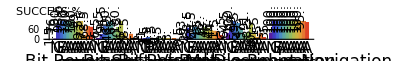

ALL_BEST_INDIRECT.pdf

```mathematica
parts = 12;
colNumber=12;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_BEST_INDIRECT.pdf",Grid[{{Style["GPAT BEST: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
(*Export["ALL_CHOICE_INDIRECT.pdf",Grid[{{Style["GPAT CHOICE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]*)
```

```mathematica
printBooleanRanksAsTable[selectedData,"SUCCESS",3]
```

ID | GPAT.FUNCTION_IMPL | RANK
3 | NC | 13/10
1 | GP | 19/10
2 | N | 14/5

## Experiments Indirect Aggregated Distance Choice

```mathematica
names={"T/HAT_G_OR_CHOICE","T/HAT_G_GP_CHOICE","T/HAT_G_NC_CHOICE","T/HAT_B_OR_CHOICE","T/HAT_B_NC_CHOICE","T/HAT_B_GP_CHOICE","T/HAT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=Flatten[Permute[Partition[sortedData,9],{2,4,3,6,1,5}],1];
aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,6]]];
printAsTable[aggregatedData,{"SOLVER","GP.TYPE","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","PROBLEM","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"}];
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.progress,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,RECO.PATTERNS}

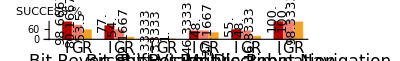

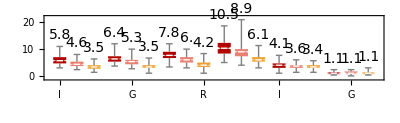

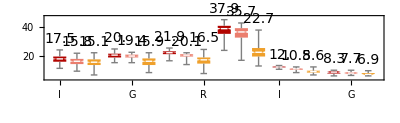

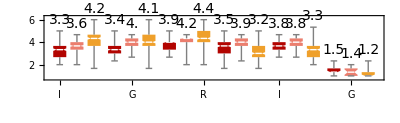

ALL_CHOICE_AGGREGATED_DISTANCE_INDIRECT.pdf

```mathematica
parts = 3;
colNumber=3;
cellAll={};

selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_DISTANCE_INDIRECT.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments Indirect Aggregated Implementation Choice

```mathematica
names={"T/HAT_G_OR_CHOICE","T/HAT_G_GP_CHOICE","T/HAT_G_NC_CHOICE","T/HAT_B_OR_CHOICE","T/HAT_B_NC_CHOICE","T/HAT_B_GP_CHOICE","T/HAT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.FUNCTION_IMPL","GPAT.DISTANCE","VARIANT","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=Flatten[Permute[Partition[sortedData,9],{2,4,3,6,1,5}],1];
aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"GP","N","NC"}&,6]]];
printAsTable[aggregatedData,{"SOLVER","GP.TYPE","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","PROBLEM","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"}];
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.progress,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,RECO.PATTERNS}

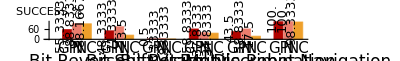

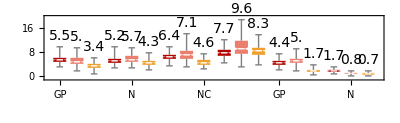

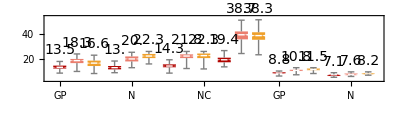

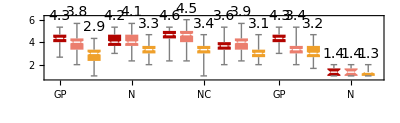

ALL_CHOICE_AGGREGATED_IMPL_INDIRECT.pdf

```mathematica
parts = 3;
colNumber=3;
cellAll={};

selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"GP","N","NC"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"GP","N","NC"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"GP","N","NC"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_IMPL_INDIRECT.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments Indirect NEAT Only

```mathematica
names={"T/HNEAT"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=Flatten[Permute[Partition[sortedData,1],{2,4,3,6,1,5}],1];
printAsTable[sortedData,{"SOLVER","GP.TYPE","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","PROBLEM","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"}]
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE}

ID | PARAM FILE | SOLVER | GP.TYPE | ID | GPAT.DISTANCE | GPAT.FUNCTION_IMPL | VARIANT | PROBLEM | RECO.GENERATOR | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT
{N} | T/HNEAT/parameters_001.txt | NEAT |  | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  | 
{N} | T/HNEAT/parameters_002.txt | NEAT |  | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  | 
{N} | T/HNEAT/parameters_003.txt | NEAT |  | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  | 
{N} | T/HNEAT/parameters_005.txt | NEAT |  | XOR |  |  |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  | 
{N} | T/HNEAT/parameters_004.txt | NEAT |  | FC |  |  |  | FC |  |  |  | 
{N} | T/HNEAT/parameters_006.txt | NEAT |  | ROBO |  |  |  | ROBOTS |  |  |  |

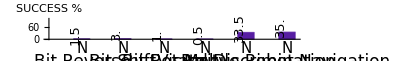

NEAT_INDIRECT.pdf

```mathematica
parts = 1;
colNumber=13;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["NEAT_INDIRECT.pdf",Grid[{{Style["NEAT Inirect: Success, Constants, Nodes",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

```mathematica
printBooleanRanksAsTable[selectedData,"SUCCESS",3]
```

ID | GPAT.FUNCTION_IMPL | RANK
3 | NC | 13/10
1 | GP | 19/10
2 | N | 14/5